```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
logticksx=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
logticksx2=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
logticksx3=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,33,2]),
{Log10@#,"",{.016,0}}&/@(10^Range[-31,33,2]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
Msunt = ToString[Subscript["M","⊙"],FormatType->StandardForm];
```

```mathematica
sigmaCi = Interpolation[{#[[1]],{#[[2]],#[[3]]}}&/@ReadList[NotebookDirectory[]<>"sigma_CDM.dat",Table[Number,{3}]],InterpolationOrder->1];
hmfC = Quiet@ReadList[NotebookDirectory[]<>"HMF_CDM.dat",Table[Number,{5}]];
hmfCi = Interpolation[{#[[1]],#[[2]],#[[3]]}&/@hmfC,InterpolationOrder->1]
dotMCi = Interpolation[{#[[1]],#[[2]],#[[4]]}&/@hmfC,InterpolationOrder->1];
```

6       17
InterpolatingFunction[{{0.01, 36.01}, {1. 10 , 1. 10  }}, <>]

```mathematica
sigmaFi = Interpolation[{#[[1]],#[[2]],{#[[3]],#[[4]]}}&/@ReadList[NotebookDirectory[]<>"sigma_FDM.dat",Table[Number,{4}]],InterpolationOrder->1]
hmfF = Quiet@ReadList[NotebookDirectory[]<>"HMF_FDM.dat",Table[Number,{6}]];
hmfFi = Interpolation[{#[[1]],#[[2]],#[[3]],#[[4]]}&/@hmfF,InterpolationOrder->1]
dotMFi = Interpolation[{#[[1]],#[[2]],#[[3]],#[[5]]}&/@hmfF,InterpolationOrder->1];
```

6           17
InterpolatingFunction[{{1., 2000.}, {1. 10 , 3.0112 10  }}, <>]

6       17
InterpolatingFunction[{{1., 2000.}, {0.01, 36.01}, {1. 10 , 1. 10  }}, <>]

```mathematica
sigmaWi = Interpolation[{#[[1]],#[[2]],{#[[3]],#[[4]]}}&/@ReadList[NotebookDirectory[]<>"sigma_WDM.dat",Table[Number,{4}]],InterpolationOrder->1]
hmfW = Quiet@ReadList[NotebookDirectory[]<>"HMF_WDM.dat",Table[Number,{6}]];
hmfWi = Interpolation[{#[[1]],#[[2]],#[[3]],#[[4]]}&/@hmfW,InterpolationOrder->1]
dotMWi = Interpolation[{#[[1]],#[[2]],#[[3]],#[[5]]}&/@hmfW,InterpolationOrder->1];
```

6           17
InterpolatingFunction[{{0.7, 40.}, {1. 10 , 3.0112 10  }}, <>]

6       17
InterpolatingFunction[{{0.7, 40.}, {0.01, 36.01}, {1. 10 , 1. 10  }}, <>]

```mathematica
sigmaEi = Interpolation[{#[[1]],#[[2]],{#[[3]],#[[4]]}}&/@ReadList[NotebookDirectory[]<>"sigma_EDM.dat",Table[Number,{4}]],InterpolationOrder->1]
hmfE = Quiet@ReadList[NotebookDirectory[]<>"HMF_EDM.dat",Table[Number,{6}]];
hmfEi = Interpolation[{#[[1]],#[[2]],#[[3]],#[[4]]}&/@hmfE,InterpolationOrder->1]
dotMEi = Interpolation[{#[[1]],#[[2]],#[[3]],#[[5]]}&/@hmfE,InterpolationOrder->1];
```

6           17
InterpolatingFunction[{{0.006, 2.}, {1. 10 , 3.0112 10  }}, <>]

6       17
InterpolatingFunction[{{0.006, 2.}, {0.01, 36.01}, {1. 10 , 1. 10  }}, <>]

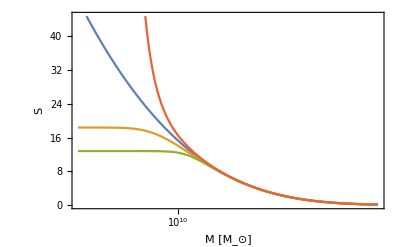

```mathematica
Plot[{sigmaCi[10^logM][[1]]^2,sigmaWi[2.0,10^logM][[1]]^2,sigmaFi[1.0,10^logM][[1]]^2,sigmaEi[0.01,10^logM][[1]]^2},{logM,7,16},FrameTicks->{Automatic,{logticksx,logticksx2}},FrameLabel->{"M ["<>Msunt<>"]","S"}]
```

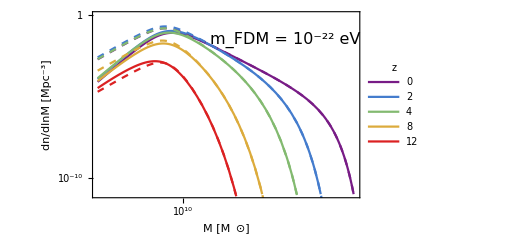

```mathematica
(* comparison with the fit of 1508.04621*)
Show[Plot[Log10[10^9hmfCi[#,10^logM](1+(10^logM/(1.6*^10 m22^(-4/3)) )^(-1.1))^(-2.2)/.m22->4.0]&/@{0.01,2,4,8,12}//Evaluate,{logM,7,16},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [Mpc^-3]"},PlotRange->{{7,16},{-11,0}},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,4]),ImageSize->380,PlotRangePadding->None,FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotLegends->LineLegend[Automatic,{0,2,4,8,12},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendMarkerSize->{10,4},LegendLabel->Style["z",14]]],
Plot[Log10[10^9hmfFi[4.0,#,10^logM]]&/@{0.01,2,4,8,12}//Evaluate,{logM,7,16},PlotStyle->(Directive[ColorData["Rainbow"][#],Dashed]&/@Subdivide[0,1,4])],
Graphics[Text[Style["m_FDM = 10^-22 eV",16],Scaled@{0.72,0.85}]]]
```

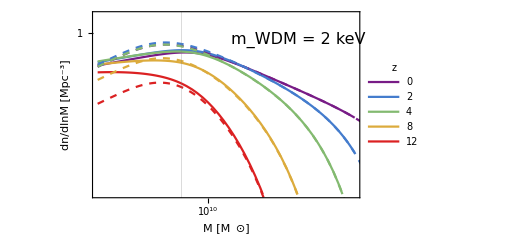

```mathematica
(* comparison with the fit of 1308.1399 *)
αW[m3_]=49/h m3^-1.11 (Ωd/0.25)^0.11 (h/0.7)^1.22/.{h->0.674,Ωd->0.2657,ρ->39.7,μ->1.12};
TW[k_,m3_]:=(1+(αW[m3] k)^(2μ))^(-5/μ)/.{h->0.674,Ωd->0.2657,ρ->39.7,μ->1.12};
Mhm[m3_]:=4Pi/3ρ (k/Pi)^-3/.First@Quiet@Solve[TW[k,m3]==1/2,k]/.{h->0.674,Ωd->0.2657,ρ->39.7,μ->1.12}
Show[Plot[Log10[10^9hmfCi[#,10^logM](1+2.7(Mhm[m3]/10^logM) )^-1.3/.m3->2.]&/@{0.01,2,4,8,12}//Evaluate,{logM,7,14},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [Mpc^-3]"},PlotRange->{{7,14},{-9,1}},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,4]),ImageSize->380,PlotRangePadding->None,FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotLegends->LineLegend[Automatic,{0,2,4,8,12},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendMarkerSize->{10,4},LegendLabel->Style["z",14]],GridLines->{{Log10@Mhm[2.]},{}}],
Plot[Log10[10^9hmfWi[2.,#,10^logM]]&/@{0.01,2,4,8,12}//Evaluate,{logM,7,16},PlotStyle->(Directive[ColorData["Rainbow"][#],Dashed]&/@Subdivide[0,1,4])],
Graphics[Text[Style["m_WDM = 2 keV",16],Scaled@{0.77,0.85}]]]
```

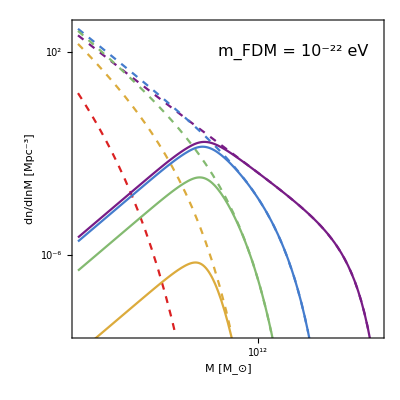
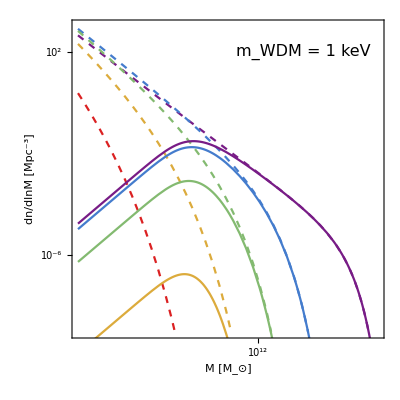
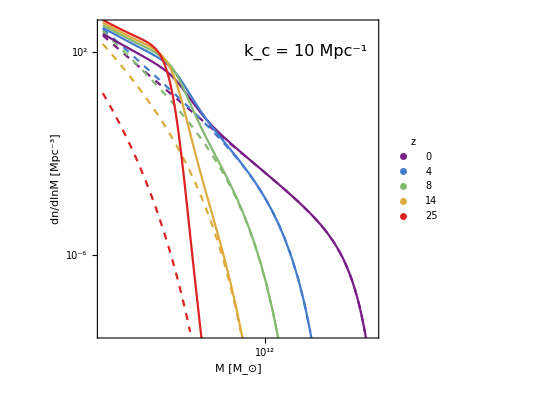

```mathematica
Row@{Show[Plot[Log10[10^9hmfCi[#,10^logM]]&/@{0.01,4,8,14,25}//Evaluate,{logM,6,17},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [Mpc^-3]"},PlotRange->{{6,16},{-9,3}},PlotStyle->(Directive[ColorData["Rainbow"][#],Dashed]&/@Subdivide[0,1,4]),AspectRatio->1,ImageSize->{Automatic,260},PlotRangePadding->None,FrameTicks->{{logticksx3,logticksx2},{logticksx3,logticksx2}},ImagePadding->{{52,12},{40,4}}],
Plot[Log10[10^9hmfFi[1.,#,10^logM]]&/@{0.01,4,8,14,25}//Evaluate,{logM,6,17},PlotStyle->(Directive[ColorData["Rainbow"][#]]&/@Subdivide[0,1,4]),PlotPoints->100],
Graphics[Text[Style["m_FDM = 10^-22 eV",16],Scaled@{0.71,0.9}]]],Show[Plot[Log10[10^9hmfCi[#,10^logM]]&/@{0.01,4,8,14,25}//Evaluate,{logM,6,17},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [Mpc^-3]"},PlotRange->{{6,16},{-9,3}},PlotStyle->(Directive[ColorData["Rainbow"][#],Dashed]&/@Subdivide[0,1,4]),AspectRatio->1,ImageSize->{Automatic,260},PlotRangePadding->None,FrameTicks->{{logticksx3,logticksx2},{logticksx3,logticksx2}},ImagePadding->{{28,12},{40,4}}],
Plot[Log10[10^9hmfWi[1.0,#,10^logM]]&/@{0.01,4,8,14,25}//Evaluate,{logM,6,17},PlotStyle->(Directive[ColorData["Rainbow"][#]]&/@Subdivide[0,1,4])],
Graphics[Text[Style["m_WDM = 1 keV",16],Scaled@{0.74,0.9}]]],
Show[Plot[Log10[10^9hmfCi[#,10^logM]]&/@{0.01,4,8,14,25}//Evaluate,{logM,6,17},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [Mpc^-3]"},PlotRange->{{6,16},{-9,3}},PlotStyle->(Directive[ColorData["Rainbow"][#],Dashed]&/@Subdivide[0,1,4]),AspectRatio->1,ImageSize->{Automatic,260},PlotRangePadding->None,FrameTicks->{{logticksx3,logticksx2},{logticksx3,logticksx2}},ImagePadding->{{28,12},{40,4}},PlotLegends->PointLegend[Automatic,{0,4,8,14,25},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendMarkerSize->12,LegendLabel->Style["z",14]]],
Plot[Log10[10^9hmfEi[0.01,#,10^logM]]&/@{0.01,4,8,14,25}//Evaluate,{logM,6,17},PlotStyle->(Directive[ColorData["Rainbow"][#]]&/@Subdivide[0,1,4])],
Graphics[Text[Style["k_c = 10 Mpc^-1",16],Scaled@{0.74,0.9}]]]}
```

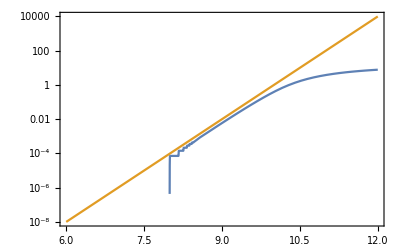

```mathematica
LogPlot[{sigmaFi[1.0,10^6][[1]]^2-sigmaFi[1.0,10^logM][[1]]^2,(10^logM/1.*^10)^(6/3)},{logM,6,12}]
```

```mathematica
S[M_]:=S0-(M/M0)^(c2/3)
Series[S'[M]/Sqrt[S[M]]/.c2->6,{M,0,2}]
FullSimplify[Sqrt[S[M]-S[2M]]/D[S[M],M],{M>0,M0>0,d>0}]//PowerExpand
Clear@S
```

-(2 M)/(M0^2 √S0)+O[M]^3

-(3 √(-1+2^(c2/3)) M^(1-c2/6) M0^(c2/6))/c2

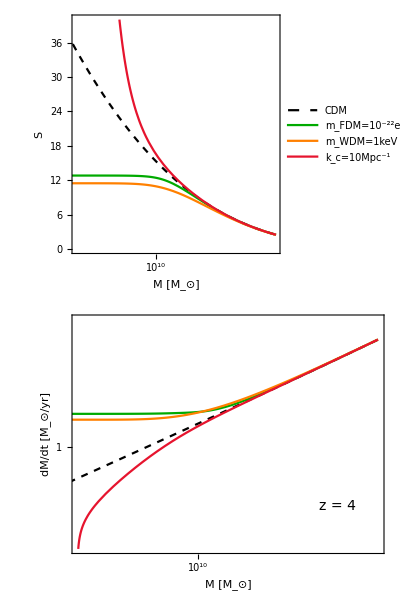

```mathematica
Column@{Plot[{sigmaCi[10^logM][[1]]^2,sigmaFi[1.,10^logM][[1]]^2,sigmaWi[1.,10^logM][[1]]^2,sigmaEi[0.01,10^logM][[1]]^2},{logM,7,13},FrameTicks->{Automatic,{logticksx,logticksx2}},PlotRange->{{8,13},{0,40}},FrameLabel->{"M ["<>Msunt<>"]","S"},AspectRatio->0.4,ImageSize->350,ImagePadding->{{52,12},{4,7}},PlotStyle->{Directive[Black,Dashed],Darker@Green,Orange,RGBColor[0.9,0.08,0.18]},PlotLegends->Placed[LineLegend[Automatic,{"CDM","m_FDM=10^-22eV","m_WDM=1keV","k_c=10Mpc^-1"},LegendMarkerSize->{15,4},LabelStyle->{FontSize->11,FontFamily->"Times"}],Scaled@{0.82,0.58}]],Show[Plot[{10^-6*dotMCi[4,10^logM],10^-6*dotMFi[1.,4,10^logM],10^-6*dotMWi[1.,4,10^logM],10^-6*dotMEi[0.01,4,10^logM]}//Log10//Evaluate,{logM,7,13},PlotRange->{{8,13},{-4,5}},FrameLabel->{"M ["<>Msunt<>"]","dM/dt ["<>Msunt<>"/yr]"},FrameTicks->{{logticksx3,logticksx2},{logticksx,logticksx2}},PlotStyle->{Directive[Black,Dashed],Darker@Green,Orange,RGBColor[0.9,0.08,0.18]},AspectRatio->0.4,ImageSize->350,ImagePadding->{{52,12},{41,8}}],Graphics[Text[Style["z = 4",14],Scaled@{0.85,0.2}]]]}
```

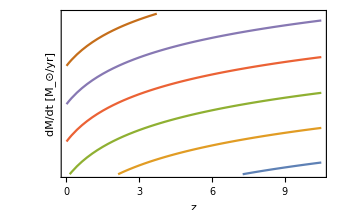
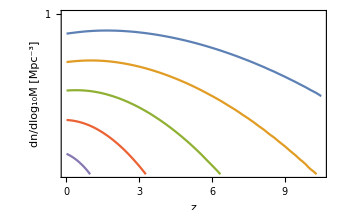

```mathematica
Row@{Plot[10^-6*dotMCi[z,10^#]&/@Range[10,15,1]//Log10//Evaluate,{z,0.01,10.5},FrameLabel->{"z","dM/dt ["<>Msunt<>"/yr]"},FrameTicks->{{logticksx,logticksx2},Automatic},ImageSize->340,PlotRange->{{0,10.5},{Log10@30.,Log10[3.*^6]}}],
Plot[Log[10]10^9hmfCi[z,10^#]&/@Range[10,15,1]//Log10//Evaluate,{z,0.01,10.5},FrameLabel->{"z","dn/dlog_10M [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},ImageSize->340,PlotRange->{{0,10.5},{-5,0}}]}
```

```mathematica
Plnmulist = ReadList[NotebookDirectory[]<>"Plnmu.dat",Table[Number,{3}]];
zlist = DeleteDuplicates[Plnmulist[[All,1]]]
Plnmulist =GatherBy[Plnmulist,First][[All,All,{2,3}]];
```

{4,5,6,7,8,9,10,11,12.5,14.5,17,25}

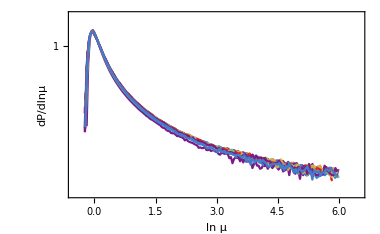

```mathematica
ListPlot[Table[{#[[1]],Log10@#[[2]]}&/@Plnmulist[[j]],{j,Length@Plnmulist}],PlotRange->{{-0.5,6.5},{-7,Log10@30}},Joined->True,FrameLabel->{"ln μ","dP/dlnμ"},PlotStyle->Join[ColorData["Rainbow"][#]&/@Subdivide[0,1,4][[1;;-2]],{Directive[Dashed,ColorData["Rainbow"][1]]}],FrameTicks->{{logticksx,logticksx2},{Automatic,Automatic}},ImageSize->380,ImagePadding->{{60,4},{40,10}}]
```

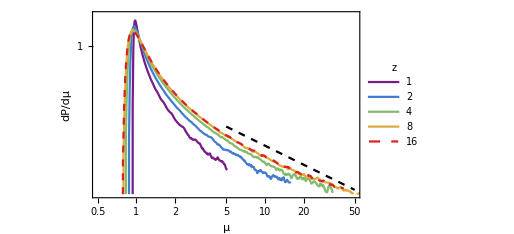

```mathematica
Show[ListLogLinearPlot[{Exp@#[[1]],Log10[#[[2]]/Exp@#[[1]]]}&/@Join[{{#[[1,1]]-0.000001,1.*^-12}},Select[#,#[[1]]<0.4&],MovingAverage[Select[#,0.4<=#[[1]]<0.8&],3],MovingAverage[Select[#,#[[1]]>=0.8&],3]]&/@Plnmulist[[1;;-1]],PlotRange->{{0.5,50},{-7,Log10@30}},Joined->True,FrameLabel->{"μ","dP/dμ"},PlotStyle->Join[ColorData["Rainbow"][#]&/@Subdivide[0,1,4][[1;;-2]],{Directive[Dashed,ColorData["Rainbow"][1]]}],FrameTicks->{{logticksx,logticksx2},{Automatic,Automatic}},PlotLegends->Placed[LineLegend[Automatic,zlist[[1;;-1]],LegendMarkerSize->{15,4},LabelStyle->{FontSize->14,FontFamily->"Times"},LegendLabel->Style["z",16]],Scaled@{0.9,0.56}],ImageSize->380,ImagePadding->{{60,4},{40,10}}],
LogLinearPlot[Log10[0.02x^-3],{x,5,50},PlotStyle->Directive[Black,Dashed]]]
```

```mathematica
fB = 0.0493/0.315
κUV[z_,γ_,zc_,f_]:=((1+f)-(1-f) Tanh[(z-zc)/γ])/2
fstar[M_,Mc_,ϵ_,α_,β_]:=If[α>0&&β>0,ϵ(α+β)/(β(M/Mc)^-α+α(M/Mc)^β),ϵ]
enh[z_,x_,ze_,z0_]:=Piecewise[{{x(z-z0)/(ze-z0),ze<z<z0},{0,z>=z0}},x];
fstar[z_,M_,Mc_,ϵ_,α_,β_,z0_,ze_]:=fstar[M,Mc,ϵ,enh[z,α,z0,ze],enh[z,β,z0,ze]]
bf = {3.92*^11,0.0613,0.877,0.405,0.214,10.63,0.426,10.45,26.18};
ρSFR1[z_]:=NIntegrate[Exp[-10^7.35/10^logM]Log[10] fstar[z,10^logM,bf[[1]],bf[[2]],bf[[3]],bf[[4]],bf[[8]],bf[[9]]]dotMCi[z,10^logM]hmfCi[z,10^logM],{logM,5,17},Method->"LocalAdaptive"]
ρSFR2[z_]:=NIntegrate[Exp[-10^7.35/10^logM]Log[10]fstar[10^logM,bf[[1]],bf[[2]],bf[[3]],bf[[4]]]dotMCi[z,10^logM]hmfCi[z,10^logM],{logM,5,17},Method->"LocalAdaptive"]
```

0.156508

```mathematica
ρMD[z_] := 0.015 (1+z)^2.7/(1+((1+z)/2.9)^5.6)
ρH[z_]:=1/(61.7(1+z)^-3.13+10^(0.22(1+z))+2.4*10^(0.5(1+z)-3.0))
```

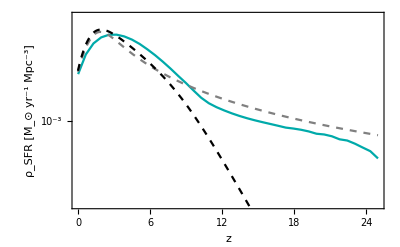

```mathematica
Show[ListPlot[{#,Log10[10^3ρSFR1[#]]}&/@Subdivide[0.01,25,39],Joined->True,FrameLabel->{"z","ρ_SFR ["<>Msunt<>" yr^-1 Mpc^-3]"},PlotRange->{{0,25},{-5,-0.5}},FrameTicks->{{logticksx,logticksx2},{Automatic,Automatic}},PlotStyle->Darker@Cyan],Plot[{Log10@ρMD[z],Log10@ρH[z]},{z,0,25},PlotStyle->{Directive[Gray,Dashed],Directive[Black,Dashed]}]]
```

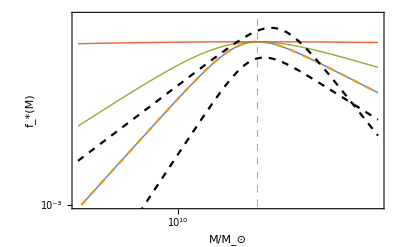

```mathematica
Show[Plot[Log10@fstar[#,10^logM,bf[[1]],bf[[2]],bf[[3]],bf[[4]],bf[[8]],bf[[9]]]-Log10@fB&/@{0,10,17,25}//Evaluate,{logM,8,14},FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotRange->{{8,14},{-3,0}},FrameLabel->{"M/"<>Msunt,"f_*(M)"},PlotStyle->{Thick,Dashed,Thick,Thick},GridLines->{{Log10[bf[[1]]]},{}},GridLinesStyle->Directive[Gray, Dashed]],
Plot[6.3*^-2/fB/((M/10^11.5)^-1.2+(M/10^11.5)^0.5)/.M->10^logM//Log10,{logM,8,14},PlotStyle->Directive[Black,Dashed]],
Plot[2 10^-0.2/((M/10^12)^-0.6+(M/10^12)^1.0)/.M->10^logM//Log10,{logM,8,14},PlotStyle->Directive[Black,Dashed]]]
```

```mathematica
WDMhist = Import[NotebookDirectory[]<>"hist_WDM.csv"];
FDMhist = Import[NotebookDirectory[]<>"hist_FDM.csv"];
EDMhist = Import[NotebookDirectory[]<>"hist_EDM.csv"];
```

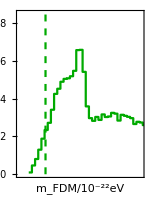
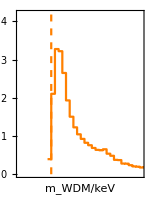
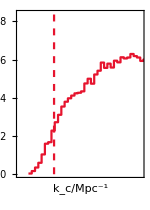

```mathematica
Row@{Show[ListPlot[FDMhist,Joined->True,InterpolationOrder->0,PlotStyle->Darker@Green,PlotRange->{{0,3},{0,0.85}},PlotRangePadding->None,FrameLabel->{"m_FDM/10^-22eV",""},FrameTicks->{Automatic,{logticksx,logticksx2}},AspectRatio->1.4,ImageSize->150,ImagePadding->{{26,9},{46,5}}],ParametricPlot[{0.65,y},{y,0,2},PlotStyle->Directive[Darker@Green,Dashed]]],
Show[ListPlot[WDMhist,Joined->True,InterpolationOrder->0,PlotStyle->Orange,PlotRange->{{Log10@0.7,Log10@12.},{0,4.2}},PlotRangePadding->None,FrameLabel->{"m_WDM/keV",""},FrameTicks->{Automatic,{logticksx,logticksx2}},AspectRatio->1.4,ImageSize->150,ImagePadding->{{26,9},{46,5}}],
ParametricPlot[{0.17,y},{y,0,5},PlotStyle->Directive[Orange,Dashed]]],Show[ListPlot[{#[[1]]+3,#[[2]]}&/@EDMhist,Joined->True,InterpolationOrder->0,PlotRange->{{0.8,3},{0,0.84}},PlotStyle->RGBColor[0.9,0.08,0.18],PlotRangePadding->None,FrameLabel->{"k_c/Mpc^-1",""},FrameTicks->{Automatic,{logticksx,logticksx2}},AspectRatio->1.4,ImageSize->150,ImagePadding->{{26,9},{46,5}}],ParametricPlot[{1.43,y},{y,0,1},PlotStyle->Directive[RGBColor[0.9,0.08,0.18],Dashed]]]}
```

```mathematica
data1 = Import[NotebookDirectory[]<>"UVLF_2102.07775.txt","Table"];
DeleteDuplicates[data1[[All,1]]]
Φ1[z_]:=Select[data1,#[[1]]==z&][[All,2;;5]]
data2 = Import[NotebookDirectory[]<>"UVLF_2108.01090.txt","Table"];
DeleteDuplicates[data2[[All,1]]]
Φ2[z_]:=Select[data2,#[[1]]==z&][[All,2;;5]]
data3 = Import[NotebookDirectory[]<>"UVLF_2403.03171.txt","Table"];
DeleteDuplicates[data3[[All,1]]]
Φ3[z_]:=Select[data3,#[[1]]==z&][[All,2;;5]]
data4 = Import[NotebookDirectory[]<>"UVLF_2503.15594.txt","Table"];
DeleteDuplicates[data4[[All,1]]]
Φ4[z_]:=Select[data4,#[[1]]==z&][[All,2;;5]]
data5 = Import[NotebookDirectory[]<>"UVLF_2504.05893.txt","Table"];
DeleteDuplicates[data5[[All,1]]]
Φ5[z_]:=Select[data5,#[[1]]==z&][[All,2;;5]]
NPDF2[x_,μ_,σp_,σm_]:= 2Piecewise[{{σm PDF[NormalDistribution[μ,σm],x],x<μ}},σp PDF[NormalDistribution[μ,σp],x]]/(σm+σp)
NPDF3[x_,μ_,σp_,σm_]:= NPDF2[Log10@x,Log10@μ,Log10[μ+σp]-Log10@σp,Log10@μ-Log10[Max[μ-σm,1.*^-20]]]
```

{4,5,6,7,8,9,10}

{4,5,6,7}

{9,10,11,12.5,14.5}

{17,25}

{17}

```mathematica
UVLC = ReadList[NotebookDirectory[]<>"data/UVluminosity_CDM1.dat",Table[Number,{6}]];
UVLC = GatherBy[UVLC,First][[All,All,2;;-1]];
UVLCi = Table[Interpolation[UVLC[[j,All,{1,5}]],InterpolationOrder->1],{j,Length@UVLC}];
```

```mathematica
UVLC2 = ReadList[NotebookDirectory[]<>"UVluminosity_CDM2.dat",Table[Number,{6}]];
UVLC2 = GatherBy[UVLC2,First][[All,All,2;;-1]];
UVLC2i = Table[Interpolation[UVLC2[[j,All,{1,5}]],InterpolationOrder->1],{j,Length@UVLC2}];
```

```mathematica
UVLC3 = ReadList[NotebookDirectory[]<>"UVluminosity_CDM3.dat",Table[Number,{6}]];
UVLC3 = GatherBy[UVLC3,First][[All,All,2;;-1]];
UVLC3i = Table[Interpolation[UVLC3[[j,All,{1,5}]],InterpolationOrder->1],{j,Length@UVLC3}];
```

```mathematica
UVLF = ReadList[NotebookDirectory[]<>"UVluminosity_FDM.dat",Table[Number,{6}]];
UVLF = GatherBy[UVLF,First][[All,All,2;;-1]];
UVLFi = Table[Interpolation[UVLF[[j,All,{1,5}]],InterpolationOrder->1],{j,Length@UVLF}];
```

```mathematica
UVLW = ReadList[NotebookDirectory[]<>"data/UVluminosity_WDM.dat",Table[Number,{6}]];
UVLW = GatherBy[UVLW,First][[All,All,2;;-1]];
UVLWi = Table[Interpolation[UVLW[[j,All,{1,5}]],InterpolationOrder->1],{j,Length@UVLW}];
```

```mathematica
UVLE = ReadList[NotebookDirectory[]<>"UVluminosity_EDM.dat",Table[Number,{6}]];
UVLE = GatherBy[UVLE,First][[All,All,2;;-1]];
UVLEi = Table[Interpolation[UVLE[[j,All,{1,5}]],InterpolationOrder->1],{j,Length@UVLE}];
```

```mathematica
Total@Flatten@Table[Log@NPDF2[10^9UVLCi[[jz]][#[[1]]],#[[2]],#[[3]],#[[4]]]&/@Join[Φ1[zlist[[jz]]],Φ2[zlist[[jz]]],Φ3[zlist[[jz]]],Φ4[zlist[[jz]]],Φ5[zlist[[jz]]]],{jz,Length@zlist}]
```

1465.26

```mathematica
Total@Flatten@Table[Log@NPDF2[10^9UVLC2i[[jz]][#[[1]]],#[[2]],#[[3]],#[[4]]]&/@Join[Φ1[zlist[[jz]]],Φ2[zlist[[jz]]],Φ3[zlist[[jz]]],Φ4[zlist[[jz]]],Φ5[zlist[[jz]]]],{jz,Length@zlist}]
```

1459.21

```mathematica
Total@Flatten@Table[Log@NPDF2[10^9UVLC3i[[jz]][#[[1]]],#[[2]],#[[3]],#[[4]]]&/@Join[Φ1[zlist[[jz]]],Φ2[zlist[[jz]]],Φ3[zlist[[jz]]],Φ4[zlist[[jz]]],Φ5[zlist[[jz]]]],{jz,Length@zlist}]
```

1441.35

```mathematica
Total@Flatten@Table[Log@NPDF2[10^9UVLFi[[jz]][#[[1]]],#[[2]],#[[3]],#[[4]]]&/@Join[Φ1[zlist[[jz]]],Φ2[zlist[[jz]]],Φ3[zlist[[jz]]],Φ4[zlist[[jz]]],Φ5[zlist[[jz]]]],{jz,Length@zlist}]
```

1462.94

```mathematica
Total@Flatten@Table[Log@NPDF2[10^9UVLWi[[jz]][#[[1]]],#[[2]],#[[3]],#[[4]]]&/@Join[Φ1[zlist[[jz]]],Φ2[zlist[[jz]]],Φ3[zlist[[jz]]],Φ4[zlist[[jz]]],Φ5[zlist[[jz]]]],{jz,Length@zlist}]
```

InterpolatingFunction::dmval: Input value {-18.24} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-17.49} lies outside the range of data in the interpolating function. Extrapolation will be used.

1467.55

```mathematica
Length@Flatten[Table[Join[Φ1[zlist[[jz]]],Φ2[zlist[[jz]]],Φ3[zlist[[jz]]],Φ4[zlist[[jz]]],Φ5[zlist[[jz]]]],{jz,Length@zlist}],1]
```

162

```mathematica
Log@%//N
```

5.0876

```mathematica
Total@Flatten@Table[Log@NPDF2[10^9UVLEi[[jz]][#[[1]]],#[[2]],#[[3]],#[[4]]]&/@Join[Φ1[zlist[[jz]]],Φ2[zlist[[jz]]],Φ3[zlist[[jz]]],Φ4[zlist[[jz]]],Φ5[zlist[[jz]]]],{jz,Length@zlist}]
```

1465.18

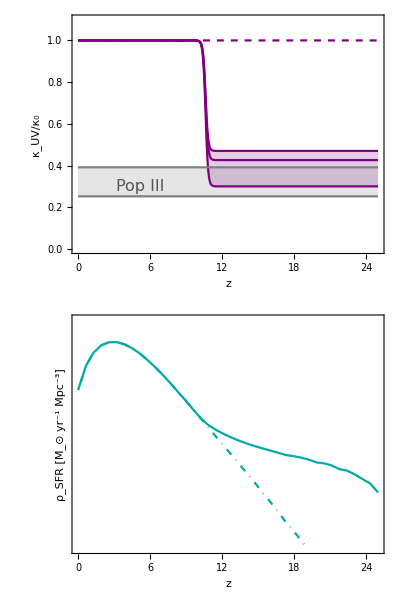
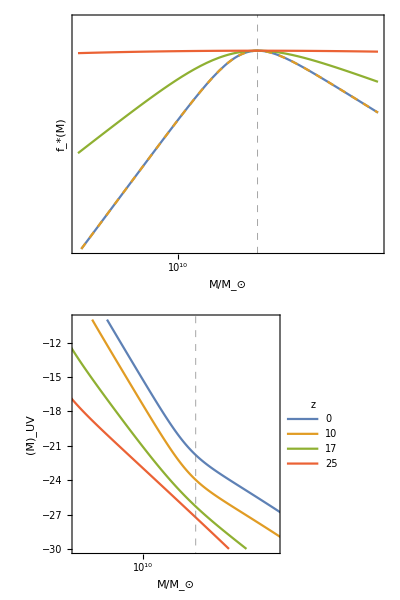

```mathematica
Row@{Column@{Show[Plot[{κUV[z,bf[[5]],bf[[6]],0.3 ],κUV[z,bf[[5]],bf[[6]],0.47],κUV[z,bf[[5]],bf[[6]],bf[[7]] ],0.29/1.15,0.45/1.15,1},{z,0,25},FrameLabel->{"z","κ_UV/κ_0"},ImageSize->{Automatic,200},PlotRange->{{0,25},{0,1.1}},ImagePadding->{{52,12},{40,10}},AspectRatio->1,PlotStyle->{Directive[Purple,Thin],Directive[Purple,Thin],Directive[Purple,Thick],Directive[Thin,Gray],Directive[Thin,Gray],Directive[Dashed,Purple]},Filling->{1->{2},4->{5}}],Graphics[Text[Style["Pop III",16,Darker@Gray],Scaled@{0.22,0.28}]]],
ListPlot[{{#,Log10[10^3ρSFR1[#]]}&/@Subdivide[0.01,25,39],{#,Log10[10^3ρSFR2[#]]}&/@Subdivide[0.01,25,39]},Joined->True,FrameLabel->{"z","ρ_SFR ["<>Msunt<>" yr^-1 Mpc^-3]"},PlotRange->{{0,25},{-5,-0.5}},FrameTicks->{{logticksx,logticksx2},{Automatic,Automatic}},PlotStyle->{Darker@Cyan,Directive[Darker@Cyan,DotDashed]},ImageSize->{Automatic,200},ImagePadding->{{52,12},{40,10}},AspectRatio->1]},Column@{Plot[Log10@fstar[#,10^logM,bf[[1]],bf[[2]],bf[[3]],bf[[4]],bf[[8]],bf[[9]]]-Log10@fB&/@{0,10,17,25}//Evaluate,{logM,8,14},FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotRange->{{8,14},{-3,0}},FrameLabel->{"M/"<>Msunt,"f_*(M)"},ImageSize->{Automatic,200},ImagePadding->{{52,12},{40,10}},PlotStyle->{Thick,Dashed,Thick,Thick},AspectRatio->1,GridLines->{{Log10[bf[[1]]]},{}},GridLinesStyle->Directive[Gray, Dashed]],
ListPlot[Table[{Log10@#[[2]],#[[1]]}&/@UVLC[[j]],{j,{1,7,11,-1}}]//Evaluate,Joined->True,FrameLabel->{"M/"<>Msunt,"(M̄)_UV"},PlotRange->{{8,14},{-30,-10}},FrameTicks->{Automatic,{logticksx,logticksx2}},PlotStyle->Thick,GridLines->{{Log10[bf[[1]]]},{}},GridLinesStyle->Directive[Gray, Dashed],ImageSize->{Automatic,200},ImagePadding->{{52,12},{40,10}},AspectRatio->1,PlotLegends->Placed[LineLegend[Automatic,{0,10,17,25},LegendLabel->Style["z",14],LegendMarkerSize->{15,3},LabelStyle->{FontSize->10,FontFamily->"Times"}],Scaled@{0.85,0.67}]]}}
```

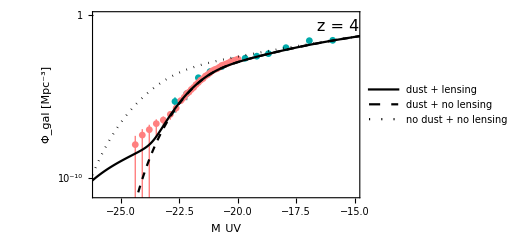

```mathematica
jz0 = 1;
P1 = Legended[Show[ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ1[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Cyan,PlotRange->{{-26,-15},{-11,0}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->DotDashed,ImageSize->380,ImagePadding->{{60,4},{40,10}}],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ2[zlist[[jz0]]]//Evaluate,PlotStyle->Pink],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ3[zlist[[jz0]]]//Evaluate,PlotStyle->Blue],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ4[zlist[[jz0]]]//Evaluate,PlotStyle->Brown],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ5[zlist[[jz0]]]//Evaluate,PlotStyle->Gray],
ListPlot[{{#[[1]],Log10[10^9#[[3]]]}&/@UVLC[[jz0]],{#[[1]],Log10[10^9#[[4]]]}&/@UVLC[[jz0]],{#[[1]],Log10[10^9#[[5]]]}&/@UVLC[[jz0]]}//Evaluate,PlotRange->{{-30,-15},{-12,-1}},Joined->True,PlotStyle->{Directive[Black,Dotted],Directive[Black,Dashed],Black}],
Graphics[Text[Style["z = "<>ToString@zlist[[jz0]],16],Scaled@{0.92,0.92}]]],Placed[LineLegend[{Black,Directive[Black,Dashed],Directive[Black,Dotted]},{"dust + lensing","dust + no lensing","no dust + no lensing"},LabelStyle->{FontSize->14,FontFamily->"Times"},LegendMarkerSize->{24,4}],Scaled@{0.74,0.2}]]
```

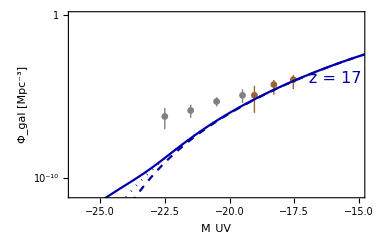

```mathematica
jz0 = -2;
P2 = Show[ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ1[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Cyan,PlotRange->{{-26,-15},{-11,0}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->DotDashed,ImageSize->380,ImagePadding->{{60,4},{40,10}}],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ2[zlist[[jz0]]]//Evaluate,PlotStyle->Pink],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ3[zlist[[jz0]]]//Evaluate,PlotStyle->Blue],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ4[zlist[[jz0]]]//Evaluate,PlotStyle->Brown],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ5[zlist[[jz0]]]//Evaluate,PlotStyle->Gray],
ListPlot[{{#[[1]],Log10[10^9#[[3]]]}&/@UVLC[[jz0]],{#[[1]],Log10[10^9#[[4]]]}&/@UVLC[[jz0]],{#[[1]],Log10[10^9#[[5]]]}&/@UVLC[[jz0]]}//Evaluate,PlotRange->{{-30,-15},{-12,-1}},Joined->True,PlotStyle->{Directive[Darker@Blue,Dotted],Directive[Darker@Blue,Dashed],Darker@Blue}],
Graphics[Text[Style["z = "<>ToString@zlist[[jz0]],16,Darker@Blue],Scaled@{0.9,0.64}]]]
```

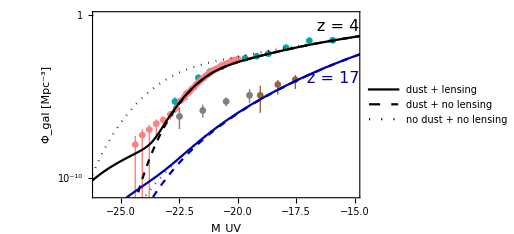

```mathematica
Show[P1,P2]
```

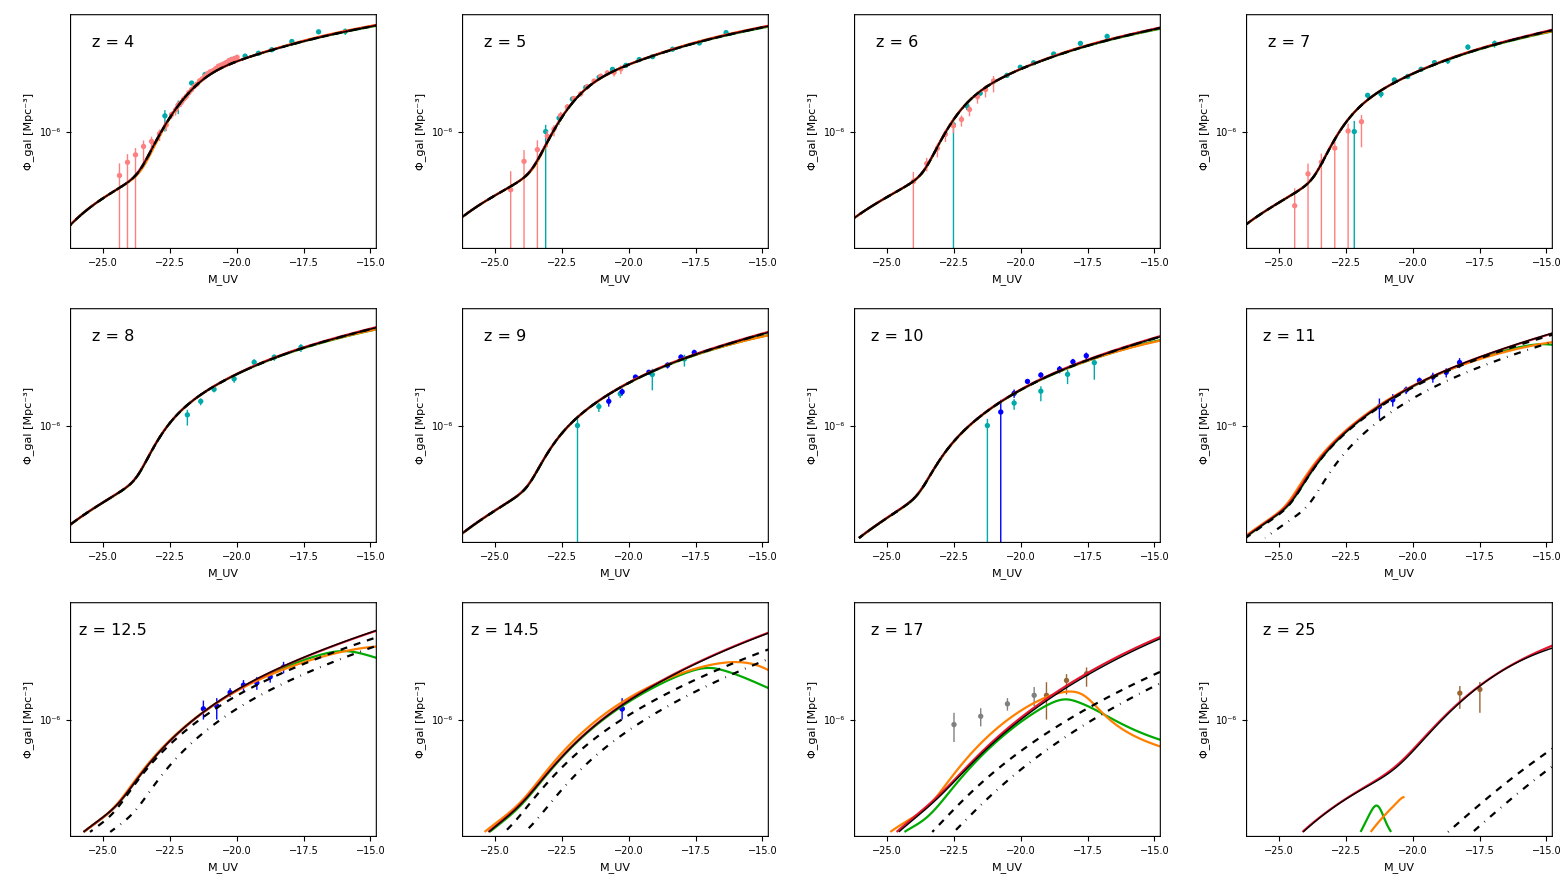

```mathematica
Grid@ArrayReshape[Table[Show[ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ1[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Cyan,PlotRange->{{-26,-15},{-11,-1}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->DotDashed,ImageSize->300],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ2[zlist[[jz0]]]//Evaluate,PlotStyle->Pink],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ3[zlist[[jz0]]]//Evaluate,PlotStyle->Blue],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ4[zlist[[jz0]]]//Evaluate,PlotStyle->Brown],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ5[zlist[[jz0]]]//Evaluate,PlotStyle->Gray],
ListPlot[{#[[1]],Log10[10^9#[[5]]]}&/@UVLF[[jz0]]//Evaluate,PlotRange->{{-26,-15},{-11,-1}},Joined->True,PlotStyle->Directive[Darker@Green]],
ListPlot[{#[[1]],Log10[10^9#[[5]]]}&/@UVLW[[jz0]]//Evaluate,PlotRange->{{-26,-15},{-11,-1}},Joined->True,PlotStyle->Directive[Orange]],ListPlot[{#[[1]],Log10[10^9#[[5]]]}&/@UVLE[[jz0]]//Evaluate,PlotRange->{{-26,-15},{-11,-1}},Joined->True,PlotStyle->Directive[RGBColor[0.9,0.08,0.18]]],
ListPlot[{#[[1]],Log10[10^9#[[5]]]}&/@UVLC[[jz0]]//Evaluate,PlotRange->{{-26,-15},{-11,-1}},Joined->True,PlotStyle->Directive[Black,Thick]],
ListPlot[{#[[1]],Log10[10^9#[[5]]]}&/@UVLC2[[jz0]]//Evaluate,PlotRange->{{-26,-15},{-11,-1}},Joined->True,PlotStyle->Directive[Black,Dashed]],
ListPlot[{#[[1]],Log10[10^9#[[5]]]}&/@UVLC3[[jz0]]//Evaluate,PlotRange->{{-26,-15},{-11,-1}},Joined->True,PlotStyle->Directive[Black,DotDashed]],
Graphics[Text[Style["z = "<>ToString@zlist[[jz0]],16],Scaled@{0.14,0.88}]]],{jz0,Length@zlist}],{3,4}]
```